```mathematica
TheImageSize = 180;
```

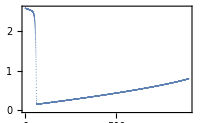

```mathematica
ExportAndShow["R(v)",ListPlot[{VvecSkipped,RTable[[;;,-1]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->MaTeX/@{"v","R(v,u=-60)"},ImageSize->TheImageSize]]
```

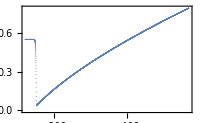

```mathematica
ExportAndShow["R(u)",ListPlot[{UvecSkipped,RTable[[-1,;;]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->MaTeX/@{"u","R(v=900,u)"},ImageSize->TheImageSize]]
```

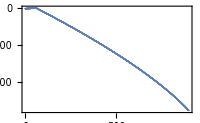

```mathematica
ExportAndShow["S(v)",ListPlot[{VvecSkipped,STable[[;;,-1]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->MaTeX/@{"v","S(v,u=-60)"},ImageSize->TheImageSize]]
```

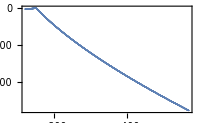

```mathematica
ExportAndShow["S(u)",ListPlot[{UvecSkipped,STable[[-1,;;]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->MaTeX/@{"u","S(v=900,u)"},ImageSize->TheImageSize]]
```

```mathematica
TvvInitial = (2D[MFunc,v]-2D[QFunc,v]QFunc/(rp/.{m->MFunc,Q->QFunc}));
```

```mathematica
(* Tuu(v,u=const)*)
```

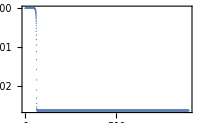
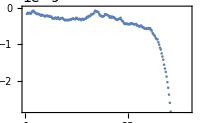

```mathematica
{ExportAndShow["Tuu(v)",ListPlot[{VvecSkipped[[3;;]],cu[[3;;,-2]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]}, PlotRange->All,ImageSize->TheImageSize]],ExportAndShow["Tuu(v upto 40)",ListPlot[{VvecSkipped[[2;;200]],cu[[2;;200,-2]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]},ImageSize->TheImageSize]]}
```

```mathematica
(*Tuu(v=const,u)*)
```

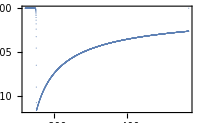
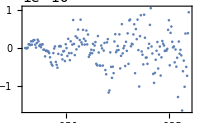

```mathematica
{ExportAndShow["Tuu(u)",ListPlot[{UvecSkipped[[2;;]],cu[[-1,2;;]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]},ImageSize->TheImageSize]],ExportAndShow["Tuu(u upto 40)",ListPlot[{UvecSkipped[[2;;200]],cu[[-1,2;;200]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]},ImageSize->TheImageSize]]}
```

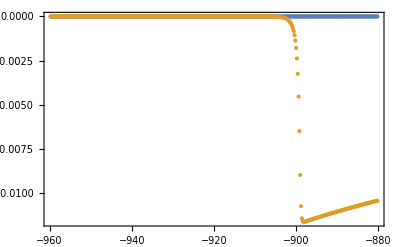

```mathematica
ListPlot[{{UvecSkipped[[2;;400]],cu[[-1,2;;400]]*0}//Transpose,{UvecSkipped[[2;;400]],cu[[-1,2;;400]]}//Transpose},PlotRange->All,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]}]
```

```mathematica
(* Tvv(v,u=const), and analytical expression for Tvv*)
```

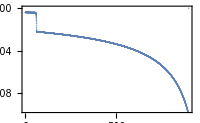

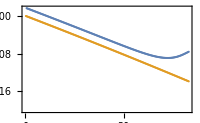

```mathematica
ExportAndShow["Tvv(v)",ListPlot[{VvecSkipped[[2;;]],cv[[2;;,-2]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]},ImageSize->TheImageSize]]
ExportAndShow["Tvv(v upto 50)",ListPlot[{{VvecSkipped[[2;;250]],Table[cv[[j,-2]],{j,2,250}]}//Transpose,{VvecSkipped[[2;;250]],Table[TvvInitial/.{v->Vvec[[(j-1)*skip+1]]},{j,2,250}]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]},PlotLegends->Placed[MaTeX/@{"\\widetilde{T}_{vv}","2M_{,v}-\\frac{2QQ_{,v}}{r}"}, Top],ImageSize->TheImageSize]]
```

```mathematica
(*Tvv(v=const, u)*)
```

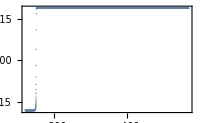
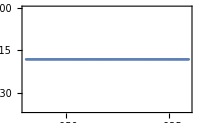

```mathematica
{ExportAndShow["Tvv(u)",ListPlot[{UvecSkipped[[3;;]],cv[[-2,3;;]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]}, PlotRange->All,ImageSize->TheImageSize]],ExportAndShow["Tvv(u upto 40)",ListPlot[{UvecSkipped[[2;;200]],cv[[-2,2;;200]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]},ImageSize->TheImageSize]]}
```

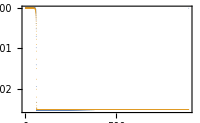

```mathematica
(*
R Tuu Mu^2:
Blue: v=const, u varies
Orange: u=const, v varies
Note: x axis isn't correct for Blue.
*)
ExportAndShow["Tuu Mu^2",ListPlot[{{VvecSkipped[[2;;]],cu[[-1,2;;]]*(MFunc/.{v->-Uvec0[[1*skip+1;;-1;;skip]]})^2}//Transpose,{VvecSkipped[[3;;]],cu[[3;;,-2]]*(MFunc/.{v->-Uvec0[[-2]]})^2}//Transpose},PlotRange->All,Frame->True,FrameLabel->{MaTeX@"v\; or\; u",Rotate[MaTeX@"\\widetilde{T}_{uu}M^u(u)^2",-90 Degree]},ImageSize->TheImageSize]]
```

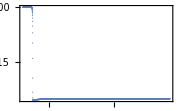

```mathematica
ExportAndShow["Tuu(u) Mu^2",ListPlot[{UvecSkipped[[2;;-2]],cu[[-1,2;;-2]]*(MFunc/.{v->-Uvec0[[1*skip+1;;-1-skip;;skip]]})^2}//Transpose,PlotRange->All,Frame->True,FrameLabel->{MaTeX@"u"(*,Rotate[MaTeX@"\\widetilde{T}_{uu}M^u(u)^2",-90 Degree]*)},ImageSize->TheImageSize]]
```

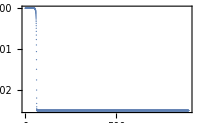

```mathematica
ExportAndShow["Tuu(v) Mu^2",ListPlot[{VvecSkipped[[3;;]],cu[[3;;,-2]]*(MFunc/.{v->-Uvec0[[-2]]})^2}//Transpose,PlotRange->All,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{uu}M^u(u)^2",-90 Degree]},ImageSize->TheImageSize]]
```

```mathematica
(*
R Tvv Mv^2:
Blue: u=const, v varies
Orange: v=const, u varies
Note: X axis isn't correct for Orange.
*)
```

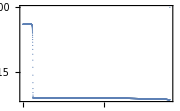

```mathematica
ExportAndShow["Tvv(v) M^2",ListPlot[{{VvecSkipped[[2;;]],cv[[2;;,-1]]*MTable[[2;;-1;;skip]]^2}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"(*,Rotate[MaTeX@"\\widetilde{T}_{vv}M^v(v)^2",-90 Degree]*)},ImageSize->TheImageSize]]
```

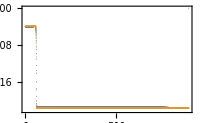

```mathematica
ExportAndShow["Tvv(v or u) M^2",ListPlot[{{VvecSkipped[[2;;]],cv[[2;;,-1]]*MTable[[2;;-1;;skip]]^2}//Transpose,{VvecSkipped[[2;;]],cv[[-2,2;;]]*MTable[[-2]]^2}//Transpose},Frame->True,FrameLabel->{MaTeX@"v\; or\; u",Rotate[MaTeX@"\\widetilde{T}_{vv}M^v(v)^2",-90 Degree]},ImageSize->TheImageSize]]
```

```mathematica
(*Region 1*)
```

```mathematica
(* Tvv and analytical expression along the initial conditions*)
```

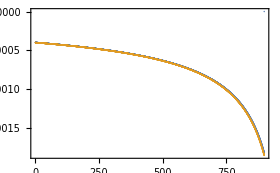

```mathematica
TvvInitial = (2D[MFunc,v]-2D[QFunc,v]QFunc/r);
ExportAndShow["Tvv(initial value)",ListPlot[{{VvecSkipped[[2;;-2]],Table[cv[[j+1,-j]],{j,2,Length[cv]-1}]}//Transpose,{VvecSkipped[[2;;-2]],Table[TvvInitial/.{v->Vvec[[(j-1)*skip+1]],r->Sqrt[RTable[[j+1,-j]]]},{j,2,Length[cv]-1}]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]},PlotLegends->Placed[MaTeX/@{"\\widetilde{T}_{vv}","2M_{,v}-\\frac{2QQ_{,v}}{r}"}, Top],ImageSize->280]]
```

```mathematica
(* Scaling of Tvv: Tvv * M^2*)
```

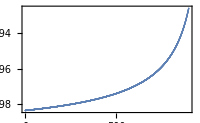

```mathematica
ExportAndShow["Tvv(initial values) M^2",ListPlot[{VvecSkipped[[2;;-3]],Table[cv[[j+1,-j]]*MTable[[(j-1)*skip+1]]^2,{j,2,Length[cv]-2}]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{vv}M(v)^2",-90 Degree]},ImageSize->TheImageSize]]
```

```mathematica
(* Tuu along initial conditions *)
```

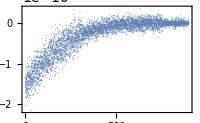

```mathematica
ExportAndShow["Tuu(initial values)",ListPlot[{VvecSkipped[[2;;-2]],Table[cu[[j+1,-j]],{j,2,Length[cv]-1}]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]},ImageSize->TheImageSize]]
```

```mathematica
(* Tvv-analytical expression along initial conditions*)
```

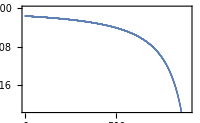

```mathematica
ExportAndShow["Tvv(v)-Analytical Expr",ListPlot[{VvecSkipped[[1;;-2]],Table[-cv[[j+1,-j]]+TvvInitial/.{v->Vvec[[(j-1)*skip+1]],r->Sqrt[RTable[[j+1,-j]]]},{j,1,Length[cv]-1}]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",MaTeX@"\\widetilde{T}_{vv}-2M_{,v}+\\frac{2QQ_{,v}}{r}"},ImageSize->TheImageSize]]
```

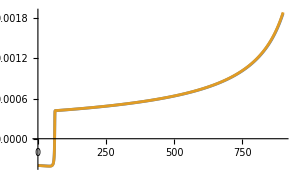

```mathematica
TvvInitial = (2D[MFunc,v]-2D[QFunc,v]QFunc/r);
ExportAndShow["Tvv(v) and vaidya expr",ListLinePlot[{{VvecSkipped[[2;;-3]],Table[cv[[j+1,-1]],{j,2,Length[cv]-2}]}//Transpose,{VvecSkipped[[2;;-2]],Table[TvvInitial/.{v->Vvec[[(j-1)*skip+1]],r->Sqrt[RTable[[j+1,-1]]]},{j,2,Length[cv]-1}]}//Transpose}, PlotLegends->Placed[MaTeX/@{"\\widetilde{T}_{vv}","2M_{,v}-\\frac{2QQ_{,v}}{r}"}, Top],PlotStyle->{Thickness[0.007],Thickness[Medium]},ImageSize->300]]
```

```mathematica
(*Region 2*)
```

```mathematica
(* R of RN (at certain v) versus computed R *)
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

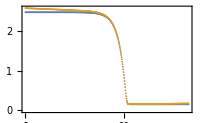

```mathematica
RNRTableU=Table[RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->-Uvec0[[-1]]},QFunc/.{v->-Uvec0[[-1]]}]^2,{j,1,500*skip,skip}];
ExportAndShow["R(v) RN",ListPlot[{{VvecSkipped[[1;;500]],RNRTableU}//Transpose,{VvecSkipped[[;;500]],RTable[[;;500,-1]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"R",-90 Degree]},PlotLegends->{"RN","Computed"},ImageSize->TheImageSize]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

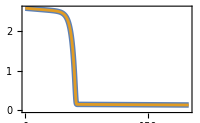

```mathematica
(* R of drifting RN versus computed R*)
endj=1000;
RNRTableU2=Table[RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->Vvec[[j]]},QFunc/.{v->Vvec[[j]]}]^2,{j,1,endj*skip,skip}];
ExportAndShow["R(v) RN drifting",ListLinePlot[{{VvecSkipped[[;;endj]],RNRTableU2}//Transpose,{VvecSkipped[[;;endj]],RTable[[;;endj,-1]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"R",-90 Degree]},PlotLegends->{"Drifting RN","Computed"},PlotStyle->{Thickness[0.02],Thickness[Medium]},ImageSize->TheImageSize]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

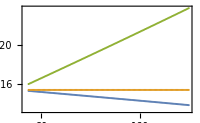

```mathematica
endj=1000;
startj=70;
skip2=5;
RNRTableU=Table[RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->-Uvec0[[-1]]},QFunc/.{v->-Uvec0[[-1]]}]^2,{j,1,endj*skip,skip*skip2}];
RNRTableU2=Table[RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->Vvec[[j]]},QFunc/.{v->Vvec[[j]]}]^2,{j,1,endj*skip,skip*skip2}];
XAxis = VvecSkipped[[startj*skip2;;endj;;skip2]];
ExportAndShow["R(v) RN drifting RN constant",ListPlot[{{XAxis,RNRTableU2[[startj;;]]}//Transpose,{XAxis,RNRTableU[[startj;;]]}//Transpose,{XAxis,RTable[[startj*skip2;;endj;;skip2,-1]]}//Transpose},PlotLegends->{"Drifting RN","Constant RN","Computed R"},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"R",-90 Degree]},ImageSize->TheImageSize]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

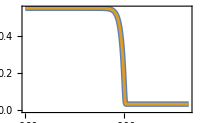

```mathematica
(*R(v=const, u) computed versus RN*)
RNRTableV=Table[RFromRStar[(Uvec0[[j]]+Vvec[[-1]])/2,MFunc/.{v->Vvec[[-1]]},QFunc/.{v->Vvec[[-1]]}]^2,{j,1,500*skip,skip}];
ExportAndShow["R(u) RN",ListLinePlot[{{UvecSkipped[[;;500]],RNRTableV}//Transpose,{UvecSkipped[[;;500]],RTable[[-1,;;500]]}//Transpose},PlotLegends->{"RN","Computed"},PlotStyle->{Thickness[0.02],Thickness[Medium]},Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"R",-90 Degree]},ImageSize->TheImageSize]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

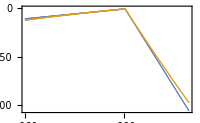

```mathematica
RNSTableU1=Log[-r f/2]/.{r->Sqrt[RTable[[-1,1;;-1;;10]]],m->MTable[[-1]],Q->QTable[[-1]]};
SApproxIndex=330;
SFinalIndex=500;
RNSTableUExact=Table[Log[-r f/2]/.{r->RFromRStar[(Uvec0[[j]]+Vvec[[-1]])/2,MFunc/.{v->Vvec[[-1]]},QFunc/.{v->Vvec[[-1]]}],m->MTable[[-1]],Q->QTable[[-1]]},{j,1,SApproxIndex*skip,skip}];
SRN=Simplify[(Log[rm/2]+Log[2κm]+Log[Δr/.Solve[rstar==RStar/.{(r-rm)->Δr}/.{r->rm},Δr][[1]]])/.{m->MTable[[-1]],Q->QTable[[-1]]}];
RNSTableUApprox=Table[SRN/.{rstar->(Uvec0[[j]]+Vvec[[-1]])/2}//N,{j,SApproxIndex*skip+1,SFinalIndex*skip,skip}];
RNSTableU=Join[RNSTableUExact,RNSTableUApprox];
ExportAndShow["S(u) RN Region2",ListPlot[{{UvecSkipped[[;;SFinalIndex]], RNSTableU}//Transpose, {UvecSkipped[[;;SFinalIndex]], STable[[-1,1;;SFinalIndex]]}//Transpose},PlotLegends->{"RN","Computed"},Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"S",-90 Degree]},ImageSize->TheImageSize]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

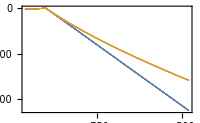

```mathematica
RNSTableU1=Log[-r f/2]/.{r->Sqrt[RTable[[-1,1;;-1;;10]]],m->MTable[[-1]],Q->QTable[[-1]]};
SApproxIndex=330;
SFinalIndex=2400;
RNSTableUExact=Table[Log[-r f/2]/.{r->RFromRStar[(Uvec0[[j]]+Vvec[[-1]])/2,MFunc/.{v->Vvec[[-1]]},QFunc/.{v->Vvec[[-1]]}],m->MTable[[-1]],Q->QTable[[-1]]},{j,1,SApproxIndex*skip,skip}];
SRN=Simplify[(Log[rm/2]+Log[2κm]+Log[Δr/.Solve[rstar==RStar/.{(r-rm)->Δr}/.{r->rm},Δr][[1]]])/.{m->MTable[[-1]],Q->QTable[[-1]]}];
RNSTableUApprox=Table[SRN/.{rstar->(Uvec0[[j]]+Vvec[[-1]])/2}//N,{j,SApproxIndex*skip+1,SFinalIndex*skip,skip}];
RNSTableU=Join[RNSTableUExact,RNSTableUApprox];
ExportAndShow["S(u) RN Region3",ListPlot[{{UvecSkipped[[;;SFinalIndex]], RNSTableU}//Transpose, {UvecSkipped[[;;SFinalIndex]], STable[[-1,1;;SFinalIndex]]}//Transpose},PlotLegends->{"RN","Computed"},Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"S",-90 Degree]},ImageSize->TheImageSize]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

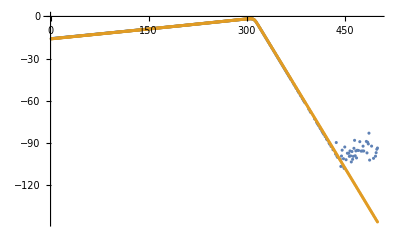

```mathematica
RNSTableV=Table[Log[-r f/2]/.{r->RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->Vvec[[j]]},QFunc/.{v->Vvec[[j]]}],m->MTable[[j]],Q->QTable[[j]]},{j,1,500*skip,skip}];
ListPlot[{RNSTableV, STable[[1;;500,-1]]}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

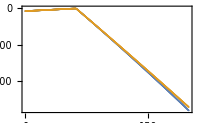

```mathematica
SApproxIndex=330;
SFinalIndex=1000;
RNSTableVExact=Table[Log[-r f/2]/.{r->RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->Vvec[[j]]},QFunc/.{v->Vvec[[j]]}],m->MTable[[j]],Q->QTable[[j]]},{j,1,SApproxIndex*skip,skip}];
SRN=Simplify[(Log[rm/2]+Log[2κm]+Log[Δr/.Solve[rstar==RStar/.{(r-rm)->Δr}/.{r->rm},Δr][[1]]])];
RNSTableVApprox=Table[SRN/.{rstar->(Uvec0[[-1]]+Vvec[[j]])/2, m->MTable[[j]],Q->QTable[[j]]}//N,{j,SApproxIndex*skip+1,SFinalIndex*skip,skip}];
RNSTableV=Join[RNSTableVExact,RNSTableVApprox];
ExportAndShow["S(v) RN Region2",ListPlot[{{VvecSkipped[[;;SFinalIndex]],RNSTableV}//Transpose, {VvecSkipped[[;;SFinalIndex]],STable[[1;;SFinalIndex,-1]]}//Transpose},PlotLegends->{"RN","Computed"},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"S",-90 Degree]},ImageSize->TheImageSize]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

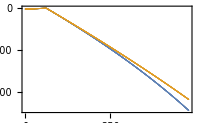

```mathematica
SApproxIndex=330;
SFinalIndex=2400;
RNSTableVExact=Table[Log[-r f/2]/.{r->RFromRStar[(Uvec0[[-1]]+Vvec[[j]])/2,MFunc/.{v->Vvec[[j]]},QFunc/.{v->Vvec[[j]]}],m->MTable[[j]],Q->QTable[[j]]},{j,1,SApproxIndex*skip,skip}];
SRN=Simplify[(Log[rm/2]+Log[2κm]+Log[Δr/.Solve[rstar==RStar/.{(r-rm)->Δr}/.{r->rm},Δr][[1]]])];
RNSTableVApprox=Table[SRN/.{rstar->(Uvec0[[-1]]+Vvec[[j]])/2, m->MTable[[j]],Q->QTable[[j]]}//N,{j,SApproxIndex*skip+1,SFinalIndex*skip,skip}];
RNSTableV=Join[RNSTableVExact,RNSTableVApprox];
ExportAndShow["S(v) RN Region3",ListPlot[{{VvecSkipped[[;;SFinalIndex]],RNSTableV}//Transpose, {VvecSkipped[[;;SFinalIndex]],STable[[1;;SFinalIndex,-1]]}//Transpose},PlotLegends->{"RN","Computed"},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"S",-90 Degree]},ImageSize->TheImageSize]]
```

```mathematica
(*Region 3*)
```

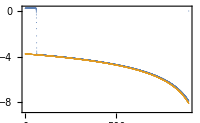

```mathematica
ExportAndShow["S,v(v) κ-",ListPlot[{{VvecSkipped,SvTable[[;;,-1]]}//Transpose,{VvecSkipped,-κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"S_{,v}","-\\kappa_-^v"},ImageSize->TheImageSize]]
```

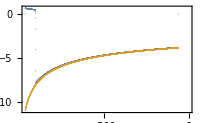

```mathematica
ExportAndShow["S,u(u) κ-",ListPlot[{{UvecSkipped,SuTable[[-1,;;]]}//Transpose,{UvecSkipped,-κm/.{m->MFunc/.{v->-Uvec0[[1;;-1;;skip]]},Q->QFunc/.{v->-Uvec0[[1;;-1;;skip]]}}}//Transpose},Frame->True,FrameLabel->{MaTeX@"u"},PlotLegends->MaTeX/@{"S_{,u}","-\\kappa_-^u"},ImageSize->TheImageSize]]
```

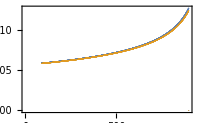

```mathematica
ExportAndShow["R,v(v) Analytical Approx",ListPlot[{{VvecSkipped[[450;;]],RvTable[[450;;,-1]]}//Transpose,{VvecSkipped[[450;;]],(-cv[[;;,-1]]/(κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}))[[450;;]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"R_{,v}","-\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}^{v}}"},ImageSize->TheImageSize]]
```

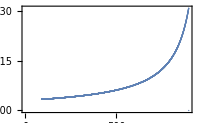

```mathematica
ExportAndShow["R,v(v)-Analytical Approx",ListPlot[{VvecSkipped[[450;;]],RvTable[[450;;,-1]]-(-cv[[;;,-1]]/(κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}))[[450;;]]}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"R_{,v}+\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}^{v}}",-90 Degree]},ImageSize->TheImageSize]]
```

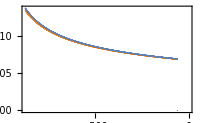

```mathematica
ExportAndShow["R,u(u) Analytical Approx",ListPlot[{{UvecSkipped[[450;;]],(-cu[[-1,;;]]/(κm/.{m->MFunc/.{v->-Uvec0[[1;;-1;;skip]]},Q->QFunc/.{v->-Uvec0[[1;;-1;;skip]]}}))[[450;;]]}//Transpose,{UvecSkipped[[450;;]],RuTable[[-1,450;;]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"u"},PlotStyle->{Orange, RGBColor[94/256,129/256,181/256]},PlotLegends->MaTeX/@{"-\\frac{\\widetilde{T}_{uu}}{\\kappa_{-}^{u}}","R_{,u}"},ImageSize->TheImageSize]]
```

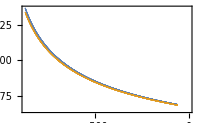

```mathematica
ExportAndShow["R,u(u) Analytical Approx run1",ListPlot[{{UvecSkipped[[450;;-2]],RuTable[[-1,450;;-2]]}//Transpose,{UvecSkipped[[450;;-2]],(-cu[[-1,;;]]/(κm/.{m->MFunc/.{v->-Uvec0[[1;;-1;;skip]]},Q->QFunc/.{v->-Uvec0[[1;;-1;;skip]]}}))[[450;;-2]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"u"},PlotLegends->MaTeX/@{"R_{,u}","-\\frac{\\widetilde{T}_{uu}}{\\kappa_{-}^{u}}"},ImageSize->TheImageSize]]
```

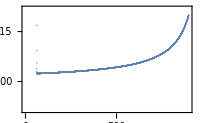

```mathematica
κmVec = -κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]};
ExportAndShow["S,v(v)-κ-",ListPlot[{VvecSkipped,SvTable[[;;,-1]]-κmVec}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"S_{,v}+\\kappa_-^v",-90 Degree]},ImageSize->TheImageSize]]
```

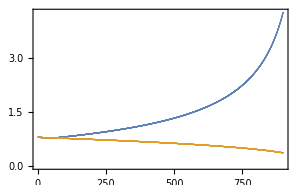

```mathematica
realQ = QTable+QuvTable*Log[1+Exp[(Uvec0[[-1]]+Vvec)*QuvScale]];
realQSkipped = realQ[[1;;-1;;skip]];
ExportAndShow["Q(v)",ListPlot[{{VvecSkipped,realQSkipped}//Transpose,{VvecSkipped,QTable[[1;;-1;;skip]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"Q",-90 Degree]},PlotLegends->MaTeX/@{"Q^v+\\delta Q","Q^v"},PlotRange->All, ImageSize->300]]
```

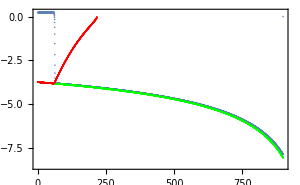

```mathematica
ExportAndShow["S,v(v) with different Q",ListPlot[{{VvecSkipped,SvTable[[;;,-1]]}//Transpose,{VvecSkipped,-κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}}//Transpose,{VvecSkipped,-κm/.{m->MTable[[1;;-1;;skip]],Q->realQSkipped}}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotStyle->{ RGBColor[94/256,129/256,181/256],Green,Red},PlotLegends->MaTeX/@{"S_{,v}","-\\kappa_-^v\\;with\\;Q^v","-\\kappa_-^v\\;with\\;\\delta Q"},ImageSize->300]]
```